Alejandro Salazar Lobos		ID: 1517982
Phys362		Assignment #5

Situation:

Red laser point of wavelength λ = 632 nm passed through a circular aperture of diameter D = 20 μm that is a distance r_0 = 20 m away from a wall/screen, where the diffraction pattern is seen:

Figure 1

The irradiance of a diffracted pattern from light passing through a circular aperture is given by:

I = (I_0((2J_1(a))/a))^2

where J_1(a) is the Bessel function of the first kind, and a = ((2π)/λ)(D/2)sin(θ).

Define II = I/I_0= ((2J_1(a))/a)^2. The amplitude is given by A = √II=(2J_1(a))/a.

To get the picture of what we would see on the wall, take a = √(a_x^2+a_y^2), with a_x= ((2π)/λ)(D/2)sin(θ_x), a_y=((2π)/λ)(D/2)sin(θ_y); for a particular ring, θ_x= θ_y. When dealing with small angles: sin(θ_i) ≈ R/r_0

⟹ R ≈r_0·sin(θ_i)

Dark fringes occur whenever the irradiance is zero, which occur when the first Bessel kind function J_1(a)=0.

Now, I will plot the amplitude and irradiance patterns :

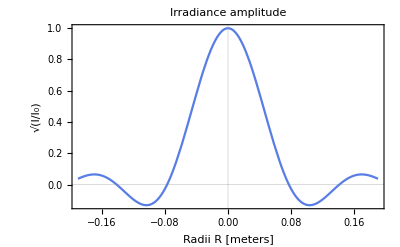

```mathematica
(* Plot the amplitude pattern *)

(* Assign values to the variables *)
diameter = 20*10^(-6);
r0=2;
lambda = 632*10^(-9);

(* Define variables *)
a = ((2*Pi)/lambda)*(diameter/2)*(R/r0);
ax = ((2*Pi)/lambda)*(diameter/2)*(Rx/r0);
ay = ((2*Pi)/lambda)*(diameter/2)*(Ry/r0);

Amplitude=(2*BesselJ[1,a])/a;
AmplitudeX=(2*BesselJ[1,ax])/ax;
AmplitudeY=(2*BesselJ[1,ay])/ay;

(* Amplitude pattern in 1D *)
Plot[Amplitude,{R,-0.19,0.19},FrameLabel->{"Radii R [meters]","√(I/I_0)"},PlotTheme->{"Scientific","BoldColor"},PlotLabel->"Irradiance amplitude"]
```

Figure 2

In Figure 2, the roots of the function correspond to the radii where the irradiance is zero. For clarity, I will plot a density function of the amplitude pattern with some radii where the irradiance is zero superimposed over it:

```mathematica
(* Calculate the radii where we get minima in irradiance *)

(* Find roots of the Bessel function of first kind *)
azero=List[N[BesselJZero[1,1]],N[BesselJZero[1,2]],N[BesselJZero[1,3]],N[BesselJZero[1,4]],N[BesselJZero[1,5]]];
```

```mathematica
(* Find the sine of the angle with respect to ray perpendicular to screen and passing throught the middle of the circular aperture *)
sinTheta=azero*(lambda/(2*Pi))*(2/diameter);
```

```mathematica
(* Find the radii of the dark fringes *)
radius = r0*sinTheta;
radiuscm = radius * 100
```

{7.70831,14.1134,20.4662,26.8035,33.1343}

We have dark fringes at R = 7.71, 14.11, 20.47, 26.80, 33.13 cm, ...(measured from the center of the main airy disk).

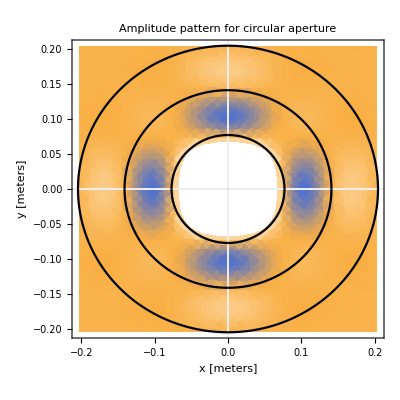

```mathematica
(* Plot the amplitude pattern as seen on the wall *)

C1 = DensityPlot[AmplitudeX AmplitudeY,{Rx,-0.203,0.203},{Ry,-0.203,0.203},FrameLabel->{"x [meters]","y [meters]"},PlotTheme->{"Scientific","BoldColor"}];

(* Dark fringes *)
C2=ParametricPlot[{radius[[1]]*Cos[t],radius[[1]]*Sin[t]},{t,0,2*Pi},PlotStyle->{Black},FrameLabel->{"x [meters]","y [meters]"},PlotTheme->{"Scientific","BoldColor"}];
C3=ParametricPlot[{radius[[2]]*Cos[t],radius[[2]]*Sin[t]},{t,0,2*Pi},PlotStyle->{Black},FrameLabel->{"x [meters]","y [meters]"},PlotTheme->{"Scientific","BoldColor"}];
C4=ParametricPlot[{radius[[3]]*Cos[t],radius[[3]]*Sin[t]},{t,0,2*Pi},PlotStyle->{Black},FrameLabel->{"x [meters]","y [meters]"},PlotTheme->{"Scientific","BoldColor"}];

Show[C1,C2,C3,C4,PlotRange->All,PlotLabel->"Amplitude pattern for circular aperture"]
```

Figure 3: Whiter parts correspond to larger positive values of the amplitude at a given time; bluer parts correspond to larger negative values of the amplitude. The black circles correspond to dark fringes, where the irradiance is zero. Compare with Figure 2 and 4. Notice that at the center, the amplitude is several times larger than at points in its neighborhood, so we get a white spot, where the graph is “saturated”.

The following code plots the irradiance pattern:

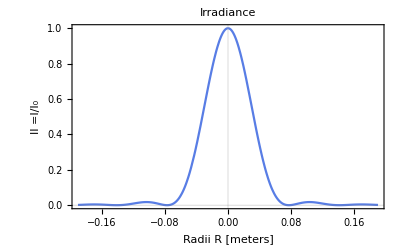

```mathematica
(* Plot the irradiance pattern *)

(* Assign values to variables *)
diameter = 20*10^(-6);
r0 = 2;
lambda = 632*10^(-9);

a = ((2*Pi)/lambda)*(diameter/2)*(R/r0);
II = ((2*BesselJ[1,a])/a)^2;

C5 =Plot[II,{R,-0.19,0.19}, FrameLabel->{"Radii R [meters]","II =I/I_0"},PlotTheme->{"Scientific","BoldColor"},PlotLabel->"Irradiance"]
```

Figure 4

Looking at Figures 2, 3, 4 together, we see consistency. The roots in Fig. 2 correspond to the points of zero irradiance in Fig. 4, whose corresponding radii are shown in Fig. 3; where we get local minima and maxima in Fig. 2, we get  local maxima in Fig. 4. In addition, the local minima and maxima in Fig. 2, corresponding the changes in color in Fig. 3.

We can plot the irradiance pattern as seen on the wall as well:

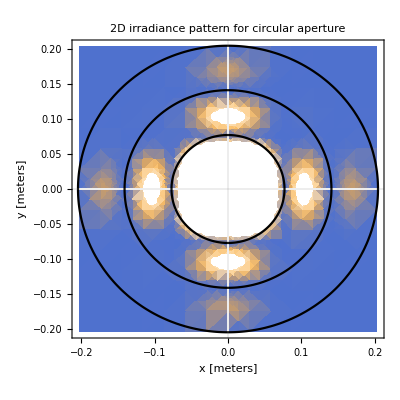

```mathematica
IIx=((2*BesselJ[1,ax])/ax)^2;
IIy=((2*BesselJ[1,ay])/ay)^2;

C5 = DensityPlot[IIx IIy,{Rx,-0.203,0.203},{Ry,-0.203,0.203},FrameLabel->{"x [meters]","y [meters]"},PlotTheme->{"Scientific","BoldColor"}];

Show[C5,C2,C3,C4,PlotRange->All,PlotLabel->"2D irradiance pattern for circular aperture"]
```

Figure 5: Similarly to Figure 3, whiter parts correspond to larger values of the irradiance. The black circles correspond to dark fringes, where the irradiance is zero. Where we get white spots, the graph is “saturated”, meaning that the value of the irradiance there is much larger than at points in the neighborhood; at the center of such white spots, we have a local maximum.